```mathematica
GraphicsGrid[Partition[Table[ArrayPlot[CellularAutomaton[n,{{1},0},{40,All}]],{n,0,63}],8],ImageSize->Full]
```

-Graphics-

```mathematica
ArrayPlot[CellularAutomaton[30,{{1},0},200]]
```

-Graphics-

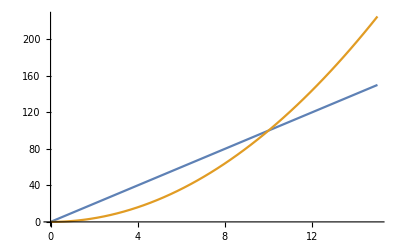

```mathematica
Plot[{10x,x^2},{x,0,15}]
```

```mathematica
Graph[Rule@@@{{3,1},{1,2},{2,3},{1,4},{4,3},{3,2}}]
```

-Graphics-

```mathematica
Rule@@@{{3,1},{1,2},{2,3},{1,4},{4,3},{3,2}}
```

{3→1,1→2,2→3,1→4,4→3,3→2}

```mathematica
f[g[x]]==g[f[x]]
```

f[g[x]]==g[f[x]]

```mathematica
FindRoot[f[g[x]]==g[f[x]],{{x,3}}]
```

FindRoot::nlnum: The function value {f[g[3.]]-1. g[f[3.]]} is not a list of numbers with dimensions {1} at {x} = {3.}.

FindRoot[f[g[x]]==g[f[x]],{{x,3}}]

```mathematica
Reduce[f[g[x]]==g[f[x]]]
```

f[g[x]]==g[f[x]]

```mathematica
FindInstance[f[g[x]]==g[f[x]],{x}]
```

FindInstance::nsmet: The methods available to FindInstance are insufficient to find the requested instances or prove they do not exist.

FindInstance[f[g[x]]==g[f[x]],{x}]

```mathematica
L[x,n,f]==f[x,n]-∑_(i=0)^∞ Subscript[λ, i] D[f[Subscript[x, 1]],{x,i}]
```

L[x,n,f]==f[x,n]-∑_(i=0)^∞ λ_i BellY[i,K[1],Table[Subscript^(K[2],0)[x,1],{K[2],1,1+i-K[1]}]] f^(K[1])[x_1]K[1]0i

```mathematica
L[x,n,f]==f[x,n]-∑_(i=1)^∞ Subscript[λ, i] D[f[Subscript[x, 1]],{x,i}]
```

L[x,n,f]==f[x,n]-∑_(i=1)^∞ λ_i BellY[i,K[1],Table[Subscript^(K[2],0)[x,1],{K[2],1,1+i-K[1]}]] f^(K[1])[x_1]K[1]0i

```mathematica
f[x,n]-∑_(i=0)^∞ Subscript[λ, i] D[f[Subscript[x, 1]],{x,i}]
```

f[x,n]-∑_(i=0)^∞ λ_i BellY[i,K[1],Table[Subscript^(K[2],0)[x,1],{K[2],1,1+i-K[1]}]] f^(K[1])[x_1]K[1]0i

```mathematica
Activate[f[x,n]-∑_(i=0)^∞ Subscript[λ, i] BellY[i,K[1],Table[Derivative[K[2],0][Subscript][x,1],{K[2],1,1+i-K[1]}]] Derivative[K[1]][f][Subscript[x, 1]]K[1]0i]
```

Table::iterb: Iterator {K[2],1,1+i-K[1]} does not have appropriate bounds.

f[x,n]-∑_(i=0)^∞ λ_i ∑_(K[1]=0)^i BellY[i,K[1],Table[Subscript^(K[2],0)[x,1],{K[2],1,1+i-K[1]}]] f^(K[1])[x_1]

```mathematica
FullSimplify[f[x,n]-∑_(i=0)^∞ Subscript[λ, i] D[f[a],{x,i}],n∈∧{x,a}∈Reals]
```

f[x,n]-f[a] λ_0

```mathematica
FullSimplify[f[x,n]-∑_(i=1)^∞ Subscript[λ, i] D[f[a],{x,i}],n∈∧{x,a}∈Reals]
```

f[x,n]

```mathematica
FullSimplify[f[x,n]-∑_(i=0)^∞ Subscript[λ, i] D[f[a],{n,i}],n∈∧{x,a}∈Reals]
```

f[x,n]-f[a] λ_0

```mathematica
FullSimplify[f[x,n]-∑_(i=1)^∞ Subscript[λ, i] D[f[a],{n,i}],n∈∧{x,a}∈Reals]
```

f[x,n]

```mathematica
FullSimplify[f[x,n]-∑_(i=1)^∞ Subscript[λ, i] D[f[a],{n,i}],n∈∧{x,a}∈Reals]
```

f[x,n]

```mathematica
FullSimplify[f[x,n]-∑_(i=1)^∞ Subscript[λ, i] D[f[a,n],{n,i}],n∈∧{x,a}∈Reals]
```

f[x,n]-∑_(i=1)^∞ λ_i f^(0,i)[a,n]

```mathematica
Grad[f[x,n]-∑_(i=1)^∞ Subscript[λ, i] Derivative[0,i][f][a,n],{x,n,Subscript[λ, i]}]
```

{f^(1,0)[x,n],-∑_(i=1)^∞ λ_i f^(0,1+i)[a,n]+f^(0,1)[x,n],-∑_(K[1]=1)^∞ i,K[1] f^(0,K[1])[a,n]}

```mathematica
Grad[f[x,n]-∑_(i=1)^∞ λ Derivative[0,i][f][a,n],{x,n,λ}]
```

{f^(1,0)[x,n],-∑_(i=1)^∞ λ f^(0,1+i)[a,n]+f^(0,1)[x,n],-∑_(i=1)^∞ f^(0,i)[a,n]}